# Coding Challenge Product of Determinants Determinant of Matrix Products

```mathematica
(* For random 3x3 matrices show that DET(AB)=DET(A)*DET(B)
   For random matrices up to 40x40 do the same in a loop 
	
This is an adaptation of the Udemy coding challenge done originally in Matlab

@author Brian Tabone
@date 12/12/2020
*)
```

### Test 3x3 random matrix determinant products and determinant of products

```mathematica
M13By3 = RandomReal[1.0 ,{3,3}];
M23by3 = RandomReal[1.0,{3,3}];
MDet1 =Abs[Det[M13By3] * Det[M23by3]];
MDet2 = Abs[Det[(M13By3 . M23by3)]];
EqTest = MDet1 - MDet2
EqRes = If[(EqTest < 1.0*10^-12), "Equal", "Not Equal"]
```

4.16334×10^-17

Equal

#### Test from 1x1 to 40x40 matrix determinant products and determinant of matrix products

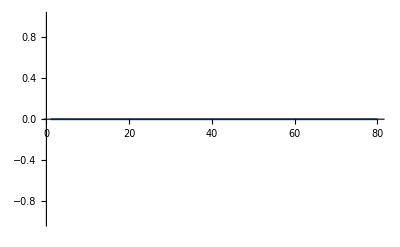

```mathematica
(* Set the upper matrix size and create empty list of results to fill out as we iterate *)
K = 80;
ResultList = RandomInteger[0,{K,2}];

For [ idx = 1, idx <= K, idx++, 
M1 = RandomInteger[100,{idx,idx}];
M2 = RandomInteger[100,{idx,idx}];
ResultList[[idx,1]] = Abs[Det[M1.M2]];
ResultList[[idx,2]] = Abs[Det[M1] * Det[M2]];
]; (* End for loop *)

Plot[(ResultList[[Floor[x],1]] - ResultList[[Floor[x],2]]), {x, 1, K}]
```